### Definitions

```mathematica
(* clear everything *)
ClearAll["Global`*"]
Remove["Global`*"]
```

```mathematica
(* Functions Definitions *)
```

```mathematica
l[z_]:=-z Log[1-ⅇ^(2π ⅈ z)]+ⅈ/2(π z^2+1/π PolyLog[2,ⅇ^(2π ⅈ z)])-(ⅈ π)/12
```

```mathematica
lAdjSU2[Δ_,u_]:=l[1-Δ]+l[1-Δ+2ⅈ u]+l[1-Δ-2ⅈ u]
```

```mathematica
uMax=1;
```

```mathematica
zSSQ[g_,a_,b_]:=Module[
{ΔQ,ΔQtilde,ΔPhi},
ΔQ=1/2+a+b;
ΔQtilde=1/2+a-b;
ΔPhi=1-2a;
NIntegrate[(Sinh[2 π u])^2 Exp[g lAdjSU2[ΔQ,u]+g lAdjSU2[ΔQtilde,u]+ lAdjSU2[ΔPhi,u]],{u,-uMax,uMax}]//Quiet
]
```

```mathematica
plotZ[deltaVec_,zVec_]:=(
data=Table[{deltaVec⟦i⟧,zVec⟦i⟧},{i,1,vecLen}];
plot1=ListPlot[data];
indMin=Position[zVec,Min[zVec]];
deltaMin=deltaVec⟦indMin⟦1⟧⟧;
plot2=ListPlot[{{deltaMin⟦1⟧,Min[zVec]}},PlotStyle->{Red,Thick,PointSize[Large]}];
Show[plot1,plot2,Frame->True,ImageSize->300,GridLines->Automatic]
)
```

### Plot integrand

```mathematica
zSSQintegrand[u_,g_,a_,b_]:=Module[
{ΔQ,ΔQtilde,ΔPhi},
ΔQ=1/2+a+b;
ΔQtilde=1/2+a-b;
ΔPhi=1-2a;
(Sinh[2 π u])^2 Exp[g lAdjSU2[ΔQ,u]+g lAdjSU2[ΔQtilde,u]+ lAdjSU2[ΔPhi,u]]
]
```

```mathematica
vecLen=20;
u1=-0.5; u2=0.9; 
xVec=u1+Range[vecLen]/vecLen*(u2-u1)+ϵ;
```

```mathematica
(* g=1 (single hypermultiplet) *)
```

Integrand as a function of u (for g=1, a=1.001, b=1.001):

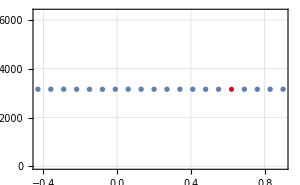

```mathematica
g=1;
a=1.001;
b=1.001;
Print["Integrand as a function of u (for g=", g, ", a=", a, ", b=", b, "):"]
zVec=Table[Abs[zSSQintegrand[u,g,a,b]],{u,1,vecLen}];
plotZ[xVec,zVec]
```

### Extremization of N=4 SU(2) gauge theories with g N=4 hypermultiplets

```mathematica
vecLen=20;
r1=-0.2; r2=0.2; 
ϵ=0.0001;
xVec=r1+Range[vecLen]/vecLen*(r2-r1)+ϵ;
a0=RandomReal[{-0.1,0.1}]
b0=RandomReal[{-0.1,0.1}]
```

-0.0758105

-0.0321633

Function of a (for b=0.0001):

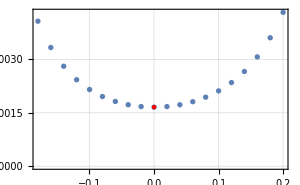

Function of b (for a=0.0001):

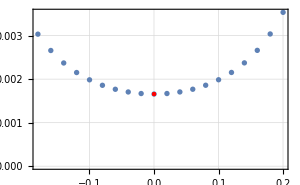

```mathematica
(* g=2 (2 hypermultiplets) *)
g=2;
Print["Function of a (for b=", ϵ, "):"]
zVec=Table[Abs[zSSQ[g,xVec⟦i⟧,ϵ]],{i,1,vecLen}];
plotZ[xVec,zVec]
Print["Function of b (for a=", ϵ, "):"]
zVec=Table[Abs[zSSQ[g,ϵ,xVec⟦i⟧]],{i,1,vecLen}];
plotZ[xVec,zVec]
```

```mathematica
g=2;
cons={Abs[a]<1,Abs[b]<1}
FindMinimum[{Abs[zSSQ[g,a,b]],cons},{a,a0},{b,b0}]
```

{Abs[a]<1,Abs[b]<1}

NIntegrate::inumr: The integrand ⅇ^(-(ⅈ π)/4-2 a Log[1-Power[«2»]]+«5»+2 («1»)+2 (-(ⅈ π)/4+(-1/2+a+Times[«2»]) Log[Plus[«2»]]+«3»+1/2 ⅈ (Times[«2»]+Times[«2»])+1/2 ⅈ (Times[«2»]+Times[«2»]))) Sinh[2 π u]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{0.00165783,{a→8.54517×10^-6,b→-2.8143×10^-9}}

Function of a (for b=0.0001):

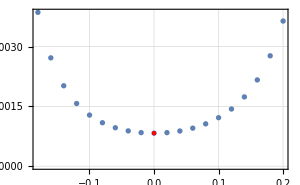

Function of b (for a=0.0001):

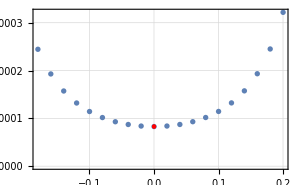

```mathematica
(* g=3 (3 hypermultiplets) *)
g=3;
Print["Function of a (for b=", ϵ, "):"]
zVec=Table[Abs[zSSQ[g,xVec⟦i⟧,ϵ]],{i,1,vecLen}];
plotZ[xVec,zVec]
Print["Function of b (for a=", ϵ, "):"]
zVec=Table[Abs[zSSQ[g,ϵ,xVec⟦i⟧]],{i,1,vecLen}];
plotZ[xVec,zVec]
```

```mathematica
g=3;
cons={Abs[a]<1,Abs[b]<1};
FindMinimum[{Abs[zSSQ[g,a,b]],cons},{a,a0},{b,b0}]
```

NIntegrate::inumr: The integrand ⅇ^(-(ⅈ π)/4-2 a Log[1-Power[«2»]]+«5»+3 («1»)+3 (-(ⅈ π)/4+(-1/2+a+Times[«2»]) Log[Plus[«2»]]+«3»+1/2 ⅈ (Times[«2»]+Times[«2»])+1/2 ⅈ (Times[«2»]+Times[«2»]))) Sinh[2 π u]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{0.0000828932,{a→0.0000131621,b→0.0000167325}}

Function of a (for b=0.0001):

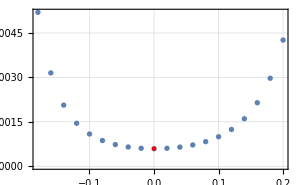

Function of b (for a=0.0001):

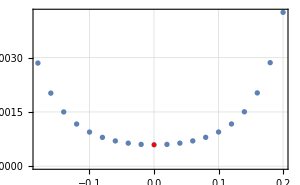

```mathematica
(* g=4 (4 hypermultiplets) *)
g=4;
Print["Function of a (for b=", ϵ, "):"]
zVec=Table[Abs[zSSQ[g,xVec⟦i⟧,ϵ]],{i,1,vecLen}];
plotZ[xVec,zVec]
Print["Function of b (for a=", ϵ, "):"]
zVec=Table[Abs[zSSQ[g,ϵ,xVec⟦i⟧]],{i,1,vecLen}];
plotZ[xVec,zVec]
```

```mathematica
g=4;
cons={Abs[a]<1,Abs[b]<1};
FindMinimum[{Abs[zSSQ[g,a,b]],cons},{a,a0},{b,b0}]
```

NIntegrate::inumr: The integrand ⅇ^(-(ⅈ π)/4-2 a Log[1-Power[«2»]]+«5»+4 («1»)+4 (-(ⅈ π)/4+(-1/2+a+Times[«2»]) Log[Plus[«2»]]+«3»+1/2 ⅈ (Times[«2»]+Times[«2»])+1/2 ⅈ (Times[«2»]+Times[«2»]))) Sinh[2 π u]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{5.92097×10^-6,{a→-0.000183368,b→-0.000255122}}